Discrete quantum walk: Details can be found in pp. 1027-1028 of Ref.: 
S. E. Venegas-Andraca, Quantum Inf Process 11, 1015 (2012).
Results can be found in Fig. 4

```mathematica
Clear["Global`*"];
ns=201;
initState=
({{1.}, {0.}})⊗Module[{mat},mat=Table[0,{ns}];mat⟦(ns+1)/2⟧=1.;mat]//Flatten;
(*e.g., opShift=({{1, 0}, {0, 0}})⊗({{0, 0, 0}, {1, 0, 0}, {0, 1, 0}})+({{0, 0}, {0, 1}})⊗({{0, 1, 0}, {0, 0, 1}, {0, 0, 0}})*)
opShift=({{1., 0}, {0, 0}})⊗DiagonalMatrix[Table[1.,{ns-1}],-1]+({{0, 0}, {0, 1.}})⊗DiagonalMatrix[Table[1.,{ns-1}],1];
opCoin=HadamardMatrix[2]⊗IdentityMatrix[ns];
opShift=opShift//ArrayFlatten;
opCoin=opCoin//ArrayFlatten;
opEvolution=opShift.opCoin;
```

```mathematica
state=MatrixPower[opEvolution,100].initState;
```

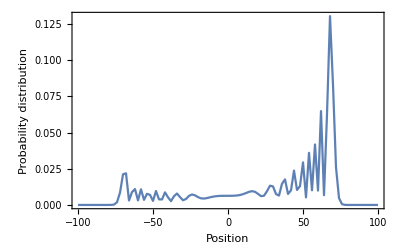

```mathematica
stateFinal=Partition[state,ns];
value=stateFinalᵀ.stateFinal//Diagonal;
ListPlot[value⟦1;;-1;;2⟧,Joined->True,PlotRange->All,DataRange->{-(ns-1)/2,(ns-1)/2},
Axes->False,Frame->True,FrameLabel->{"Position", "Probability distribution"}]
```